# Round-wire analytical calibration

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## Model, inputs and scope

∇.b2Ez−jωμσEz=0; Zint=κ I0(κa)/(2πaσ I1(κa))

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

Change frequency/current; compare independent current and Joule integrals.

## Derivation and interpretation

For a homogeneous, long cylindrical conductor, symmetry leaves Ez(r) and Jz=σEz. Combining Ampère and Faraday laws with exp(+jωt) gives (1/r)d(r dEz/dr)/dr=jωμσEz. The regular solution is C I0(κr), κ.b2=jωμσ.

Normalize C using 2π∫Jz r dr=It. The terminal voltage gradient gives Zint=κ I0(κa)/(2πaσ I1(κa)). Independently integrate ∫|J|.b2/σ dA and compare with |It|.b2 Re Zint. RMS phasors introduce no extra factor 1/2.

As κa→0, I0→1 and I1→κa/2, giving Rdc=1/(σπa.b2). The model excludes end effects and return-path external inductance. Q1 uses a=1 mm and remains a calibration case.

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## Editable parameters

```mathematica
parameters=<|"frequency_Hz"->200000.,"current_RMS_A"->20.|>;parameters
```

<|frequency_Hz -> 200000., current_RMS_A -> 20.|>

## Independent execution and results

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"wolfram-analytic",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_wolfram_analytic_20261014074541_35c79bc2, 
 
>   source_model -> wolfram-analytic, execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

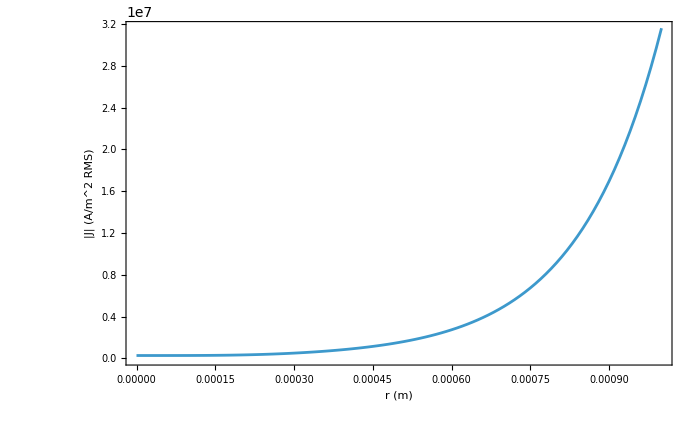

```mathematica
LitzNotebook`DisplayResearch[research]
```

## Acceptance and continuation

Inspect checks, execution_status and physical_acceptance_status. Continue full convergence and structural studies through the route README.

Sources: BESSEL; references/library.bib and references/sources.json

## Historical evidence

data/evidence/v1.0.0-rc.1/; litz-research data fetch analytic